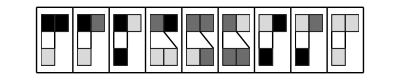
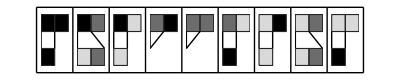
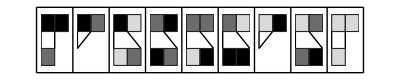
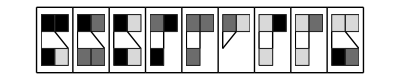
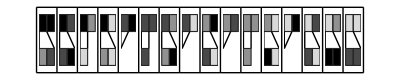
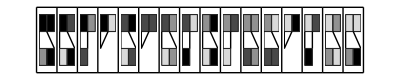

```mathematica
Table[GraphicsRow[With[{statePlot=Function[{state,pos},MapIndexed[{GrayLevel[0.85 (1-#1/Max[Keys[rule]])],EdgeForm[GrayLevel[0.15]],Rectangle[pos+{First[#2]-1,0}]}&,state]]},Graphics[{statePlot[Keys[#1],{0,0}],Line[{{0,0},{0,-1}}],Line[{{1,0},{Length[Values[#1]],-1}}],statePlot[Values[#1],{0,-2}]},]]&/@rule,],{rule,{{{2,2}->{0},{2,1}->{0},{2,0}->{2},{1,2}->{0,0},{1,1}->{0,1},{1,0}->{1,1},{0,2}->{2},{0,1}->{2},{0,0}->{0}},{{2,2}->{2},{2,1}->{0,1},{2,0}->{0},{1,2}->{},{1,1}->{},{1,0}->{2},{0,2}->{0},{0,1}->{0,1},{0,0}->{2}},{{2,2}->{1},{2,1}->{},{2,0}->{0,1},{1,2}->{2,1},{1,1}->{0,2},{1,0}->{2,2},{0,2}->{},{0,1}->{1,2},{0,0}->{0}},{{2,2}->{2,0},{2,1}->{1,1},{2,0}->{2,0},{1,2}->{2},{1,1}->{1},{1,0}->{},{0,2}->{0},{0,1}->{0},{0,0}->{2,1}},{{3,3}->{1,2},{3,2}->{2,3},{3,1}->{0},{3,0}->{1,0},{2,3}->{},{2,2}->{2},{2,1}->{1,3},{2,0}->{},{1,3}->{2,0},{1,2}->{},{1,1}->{1},{1,0}->{3,0},{0,3}->{},{0,2}->{2,0},{0,1}->{3,3},{0,0}->{2,2}},{{3,3}->{1,3},{3,2}->{0,3},{3,1}->{2},{3,0}->{},{2,3}->{0,2},{2,2}->{},{2,1}->{0,1},{2,0}->{3},{1,3}->{0,3},{1,2}->{0},{1,1}->{2,1},{1,0}->{2,2},{0,3}->{},{0,2}->{3},{0,1}->{1,0},{0,0}->{1,3}}}}]
```